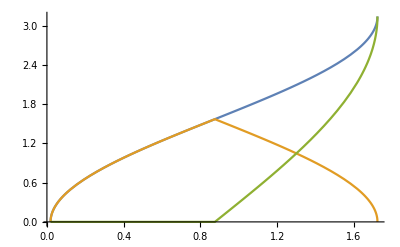

-Graphics-

```mathematica
T1[r_]:= 
π/2 -ArcTan[(B(e-r)-A(r-b))/(2 Sqrt[A B]Sqrt[(e-r)(r-b)])]
T2[r_]:=ArcSin[(2 Sqrt[A B]Sqrt[(e-r)(r-b)])/(B(e-r)+A(r-b))]
Plot[{T1[x],T2[x],T1[x]-T2[x]},{x,b,e}]
```

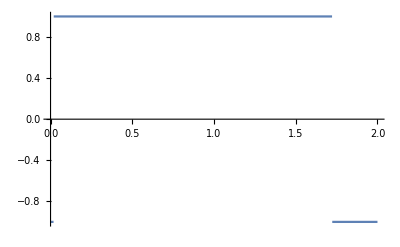

```mathematica
Plot[Sign[(e/r-1)(1-b/r) ],{r,0,2}]
```

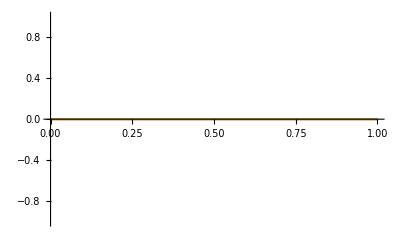

```mathematica
Plot[{Im@T1[x],Im@T2[x]},{x,0,1}]
```

```mathematica
T2'[xSUB[0.2]]
```

0.0207634

```mathematica
chi
```

0.8754

```mathematica
KZ2
```

0.000164676